```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];


numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
ListPlot[SolveForce["energysep.txt"], PlotRange->All]
ListPlot[allData,Joined->True]
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
Plot[force[x],{x,100, 1000}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl,surface20.gpl,surface21.gpl,surface22.gpl,surface23.gpl,surface24.gpl,surface25.gpl,surface26.gpl,surface27.gpl,surface28.gpl,surface29.gpl,surface30.gpl,surface31.gpl,surface32.gpl,surface33.gpl,surface34.gpl,surface35.gpl,surface36.gpl,surface37.gpl,surface38.gpl,surface39.gpl,surface40.gpl,surface41.gpl,surface42.gpl,surface43.gpl,surface44.gpl,surface45.gpl,surface46.gpl,surface47.gpl,surface48.gpl,surface49.gpl,surface50.gpl,surface51.gpl,surface52.gpl,surface53.gpl,surface54.gpl,surface55.gpl,surface56.gpl,surface57.gpl,surface58.gpl,surface59.gpl,surface60.gpl,surface61.gpl,surface62.gpl,surface63.gpl,surface64.gpl,surface65.gpl,surface66.gpl,surface67.gpl,surface68.gpl,surface69.gpl,surface70.gpl,surface71.gpl,surface72.gpl,surface73.gpl,surface74.gpl,surface75.gpl,surface76.gpl,surface77.gpl,surface78.gpl,surface79.gpl,surface80.gpl,surface81.gpl,surface82.gpl,surface83.gpl,surface84.gpl,surface85.gpl,surface86.gpl,surface87.gpl,surface88.gpl,surface89.gpl,surface90.gpl,surface91.gpl,surface92.gpl,surface93.gpl,surface94.gpl,surface95.gpl,surface96.gpl,surface97.gpl,surface98.gpl,surface99.gpl,surface100.gpl,surface101.gpl,surface102.gpl,surface103.gpl,surface104.gpl,surface105.gpl,surface106.gpl,surface107.gpl,surface108.gpl,surface109.gpl,surface110.gpl,surface111.gpl,surface112.gpl,surface113.gpl,surface114.gpl,surface115.gpl,surface116.gpl,surface117.gpl,surface118.gpl,surface119.gpl,surface120.gpl,surface121.gpl,surface122.gpl,surface123.gpl,surface124.gpl,surface125.gpl,surface126.gpl,surface127.gpl,surface128.gpl,surface129.gpl,surface130.gpl,surface131.gpl,surface132.gpl,surface133.gpl,surface134.gpl,surface135.gpl,surface136.gpl,surface137.gpl,surface138.gpl,surface139.gpl,surface140.gpl,surface141.gpl,surface142.gpl,surface143.gpl,surface144.gpl,surface145.gpl,surface146.gpl,surface147.gpl,surface148.gpl,surface149.gpl,surface150.gpl,surface151.gpl,surface152.gpl,surface153.gpl,surface154.gpl,surface155.gpl,surface156.gpl,surface157.gpl,surface158.gpl,surface159.gpl,surface160.gpl,surface161.gpl,surface162.gpl,surface163.gpl,surface164.gpl,surface165.gpl,surface166.gpl,surface167.gpl,surface168.gpl,surface169.gpl,surface170.gpl,surface171.gpl,surface172.gpl,surface173.gpl,surface174.gpl,surface175.gpl,surface176.gpl,surface177.gpl,surface178.gpl,surface179.gpl,surface180.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{}

-Graphics-

-Graphics-

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

-Graphics-

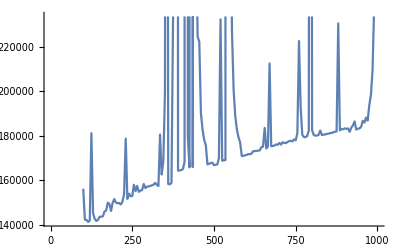

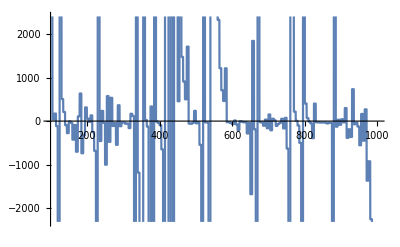

```mathematica
63721*^8}qstat
```

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["LightTerrain"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.5]];
prettyData
]
prettySurface["surface132.gpl"]
```

-Graphics3D-